Test for pairwise different distances (should be 0):  0

Visited  10  {{0.136873,0.662183},{0.77065,0.908998},{0.099012,0.644006},{0.0747849,0.711588},{0.417849,0.475834},{0.466013,0.146717},{0.494827,0.421237},{0.418441,0.00420624},{0.914883,0.921726},{0.18339,0.548094}}

Not visited  6  {{0.0452213,0.368721},{0.0981768,0.793929},{0.144233,0.0127273},{0.281567,0.342023},{0.522212,0.630813},{0.850147,0.131827}}

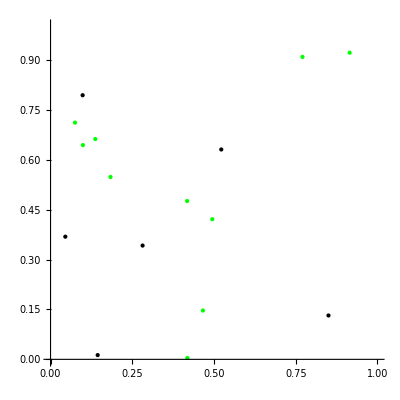

```mathematica
(* Neighbours random *)

t=Table[{Random[],Random[]},{i,16}];

n=Length[t];

td=Table[ReplacePart[Table[EuclideanDistance[t[[i]],t[[j]]],{j,n}],i->2.],{i,n}];
Print["Test for pairwise different distances (should be 0):  ",Length[Union[Drop[Sort[Flatten[td]],-n]]]-Binomial[n,2]]
tdmin=Table[Min[ReplacePart[Table[EuclideanDistance[t[[i]],t[[j]]],{j,n}],i->2.]],{i,n}];
tposition=Union[Flatten[Table[Position[td[[i]],tdmin[[i]]],{i,n}]]];

t2=Table[t[[tposition[[m]]]],{m,Length[tposition]}];
t1=Complement[t,t2];
Print["Visited  ",Length[t2],"  ",t2]
Print["Not visited  ",Length[t1],"  ",t1]
Show[ListPlot[t1,PlotStyle->{Black,PointSize[Large]}],ListPlot[t2,PlotStyle->{Green,PointSize[Large]}],PlotRange->{{0,1},{0,1}},AspectRatio->1,AxesOrigin->{0,0}]
```